```mathematica
MyAccLast[tuple_] :=MyAccLast[tuple]=Module[
{current=0, i, list=GoodForTuple[tuple]},
Monitor[
For[i=1,i<Length[list], i++,
If[list[[i]]+1==list[[i+1]],current+=1];
],
{tuple,i}];
current/Length[list]
]
```

```mathematica
CloseStreams[]
```

```mathematica
MyRatio[tuple_]:=Product[(p-1)/(p+1),{p,tuple}]
```

```mathematica
FullSimplify[((p+1)/2 -1)/((p+1)/2)]
```

(-1+p)/(1+p)

```mathematica
MyRatio[{3,5,7}]
```

1/4

```mathematica
Clear[MyAccLast]
```

```mathematica
res=Table[
{tuple, MyAccLast[tuple]},
{tuple,Select[
Prime[Subsets[Range[2,8],{2,4}]],
magicGraham[#]>0&]}
]
```

{{{3,5},167009/500500},{{3,7},7509/20000},{{3,11},41631/100000},{{3,13},42819/100000},{{3,17},44463/100000},{{3,19},5627/12500},{{5,7},250003/500000},{{5,11},55557/100000},{{5,13},57229/100000},{{5,17},14807/25000},{{5,19},29971/50000},{{7,11},62539/100000},{{7,13},3213/5000},{{7,17},8333/12500},{{7,19},67607/100000},{{11,13},35699/50000},{{11,17},4631/6250},{{11,19},74991/100000},{{13,17},19033/25000},{{13,19},7713/10000},{{17,19},79843/100000},{{3,5,7},2508251/10035455},{{3,5,11},27809/100000},{{3,5,13},5719/20000},{{3,5,17},14907/50000},{{3,5,19},15017/50000},{{3,7,11},15651/50000},{{3,7,13},32173/100000},{{3,7,17},8293/25000},{{3,7,19},2109/6250},{{3,11,13},35827/100000},{{3,11,17},37141/100000},{{3,11,19},9359/25000},{{3,13,17},7623/20000},{{3,13,19},38597/100000},{{3,17,19},10047/25000},{{5,7,11},266693/639970},{{5,7,13},42769/100000},{{5,7,17},44531/100000},{{5,7,19},9003/20000},{{5,11,13},4769/10000},{{5,11,17},989/2000},{{5,11,19},10021/20000},{{5,13,17},12699/25000},{{5,13,19},51407/100000},{{5,17,19},53329/100000},{{7,11,13},9875151/18434722},{{7,11,17},55589/100000},{{7,11,19},56283/100000},{{7,13,17},28579/50000},{{7,13,19},58063/100000},{{7,17,19},30001/50000},{{11,13,17},1109492/1746851},{{11,13,19},32187/50000},{{11,17,19},66559/100000},{{13,17,19},1391147/2026869},{{7,11,13,19},1800/3773},{{7,11,17,19},4374/8725},{{7,13,17,19},12863/25000},{{11,13,17,19},551105/964341}}

```mathematica
ListPlot[
Table[
Table[{magicGraham[tuple],MyRatio[tuple]},
{tuple,Select[
Prime[Subsets[Range[2,25],{length}]],
magicGraham[#]>0&]}],
{length,2,6}
],PlotRange->All]
```

$Aborted

```mathematica
MyRatio[{23,29,31,37}]
```

231/304

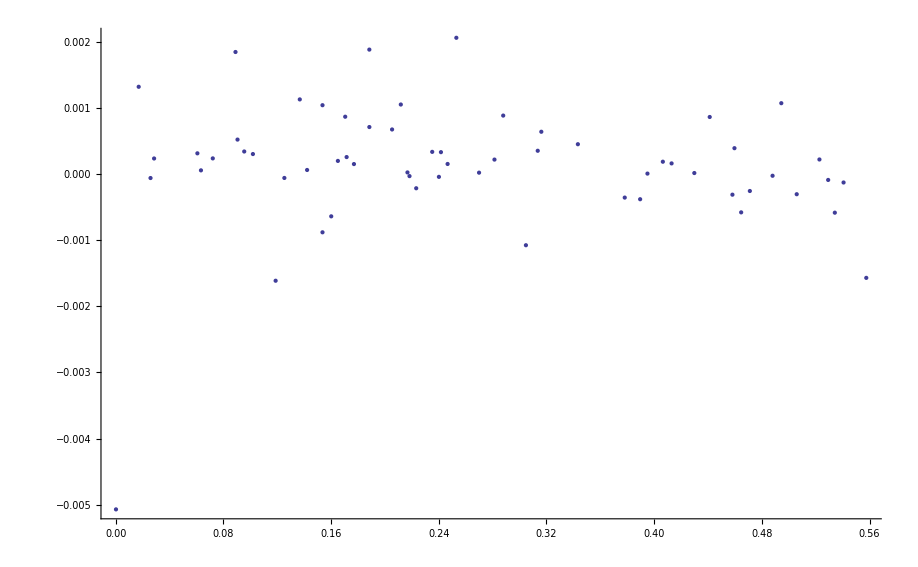

```mathematica
ListPlot[Sort[Map[{N[magicGraham[#[[1]]]],#[[2]]-MyRatio[#[[1]]]}&,res]],PlotRange->All]
```

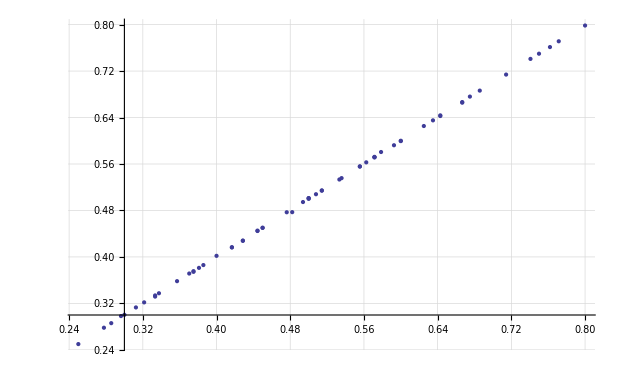

```mathematica
ListPlot[Sort[Map[Tooltip[{N[MyRatio[#[[1]]]],#[[2]]},#[[1]]]&,res]],PlotRange->All, GridLines->Automatic]
```

```mathematica
Monitor[
Table[
CalcGoodForTuple[tuple,100000],
{tuple,Sort[Select[
Prime[Subsets[Range[2,9],{2,4}]],
magicGraham[#]>0&],magicGraham[#1] > magicGraham[#2]&]}
],
tuple
]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

Aborted at value : 79995

$Aborted

```mathematica
magicGraham[tuple]
```

1+∑_p^tuple Log[(1+p)/(2 p)]/Log[p]

```mathematica
Rationalize[N[magicGraham[{3,5,7,398328266023}]],0.0000000000000001]
```

1/28503795109939

```mathematica
Convergents[N[magicGraham[{3,5,7,398328266023}]],10]
```

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 10 terms.

{0,1/28503795109939,1/28503795109940,6/171022770659639}

```mathematica
Convergents[N[magicGraham[{3,5,7,11}]],10]
```

{0,-1/4,-2/9,-5/22,-22/97,-93/410,-394/1737,-1669/7358,-32105/141539,-836399/3687372}

```mathematica
Solve[Log[(1+p)/(2p)]/Log[p]==-0.3135359480574428,p]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

```mathematica
FindRoot[Log[(1+p)/(2 p)]/Log[p]==-magicGraham[{3,5,7,398328266023}],{p,10^400},MaxIterations->1000]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{p→2.46993291800583×10^1441}

```mathematica
Module[{p, limit=IntegerPart[2.4699329180058263341371064936139794`15.954589770191005*^1441]},
For[p=limit,p≤limit+1000, p++,
If[PrimeQ[p], Print[p]]
]
]
```

24699329180058263341371064936139794025867516683645050469918740297184792303984903603566895533534658525108677500394494726237101584661442490513793177277583983248268499924398248829636674129007896832451786769182884644494920818597753423373610571272017681035638819830323804325914004779281928552469738186033057746202533848575565454246918263814592032514984536035124218417319046583471065270921421527991795344629302868551391242451404018831359556917903205909182061225823170871308113465640895666063316594495801658606926187172763908223436715176103311927543850880320960151251205769867511032415365934333076374960067407591214793522082527674517736372220538999553996105840039575655326595277983033148130560209184732420132354594945741772888350496968401192088522837396544051384859907721639567662632584345490004772708737793818118696209657778312482925971334325373139840745101172365323068756763677879888077686430694994766873054684485756583163540897378405594454340138925025518552975803670422603035436177436307647120812521383068831318052857575110708493372674212905820507205219795739271532211887941143182174248668278242362830774448126629777384805978415959952996394448335934338365055367469206339460851923678534407176188119063453639055712851542210011483747545327265684264543484747090618957289982232075713884355722640138620929033346602466476531123844110197095475728983433323889132150585355780686358052028348004416433777119918047681647520636587400832137642020301535495324321

```mathematica
PrimeQ[28503795109939]
```

True

```mathematica
N[magicGraham[{3,5,71,83}]]
```

0.0000572087

```mathematica
Sort[Select[
Prime[Subsets[Range[2,25],{4}]],
magicGraham[#]>0&],magicGraham[#1] > magicGraham[#2]&]
```

{{3,5,71,83},{3,5,67,89},{7,11,13,19},{3,7,37,73},{3,13,17,61},{3,7,43,61},{5,7,17,53},{3,11,23,53},{3,11,19,71},{3,11,31,37},{3,5,73,83},{3,13,29,31},{3,7,31,97},{3,13,19,53},{5,7,13,89},{3,11,17,89},{3,11,19,73},{3,7,41,67},{3,13,23,41},{3,11,29,41},{3,5,71,89},{5,7,19,47},{3,7,47,59},{3,5,67,97},{5,7,23,37},{3,7,37,79},{3,17,23,29},{3,5,73,89},{3,5,79,83},{3,13,17,67},{3,7,43,67},{3,7,41,71},{3,17,19,37},{5,11,13,37},{3,13,23,43},{3,7,47,61},«10064»,{67,73,83,89},{67,71,79,97},{59,73,89,97},{71,73,79,89},{53,83,89,97},{61,71,89,97},{59,79,83,97},{67,73,79,97},{61,73,89,97},{67,71,83,97},{61,79,83,97},{71,73,83,89},{67,79,83,89},{67,73,83,97},{59,79,89,97},{71,73,79,97},{67,71,89,97},{61,79,89,97},{59,83,89,97},{71,79,83,89},{71,73,83,97},{67,73,89,97},{67,79,83,97},{73,79,83,89},{61,83,89,97},{71,73,89,97},{71,79,83,97},{67,79,89,97},{73,79,83,97},{67,83,89,97},{71,79,89,97},{73,79,89,97},{71,83,89,97},{73,83,89,97},{79,83,89,97}}

```mathematica
ListPlot[Take[GoodForTuple[{7,11,13,23}],{130,140}]]
```

-Graphics-

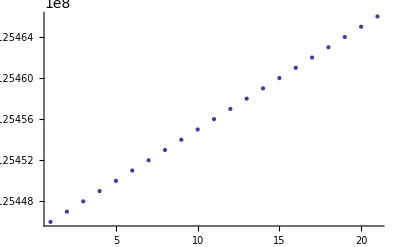

```mathematica
ListPlot[Take[GoodForTuple[{67,73,83,89}],{6340,6360}]]
```

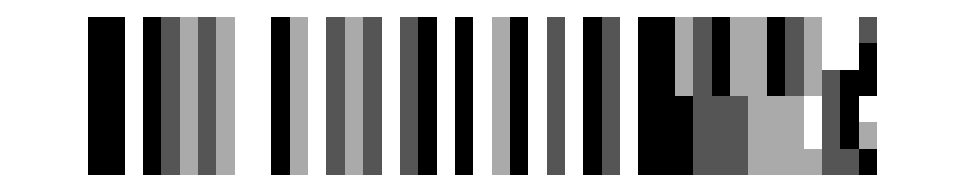

```mathematica
ArrayPlot[Map[IntegerDigits[#,7]&,Take[GoodForTuple[{7,11,13,23}],{130,135}]]]
```

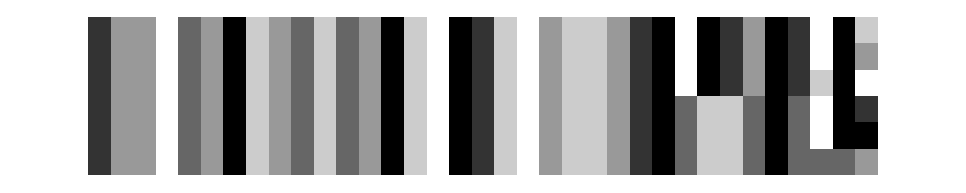

```mathematica
ArrayPlot[Map[IntegerDigits[#,11]&,Take[GoodForTuple[{7,11,13,23}],{130,135}]]]
```

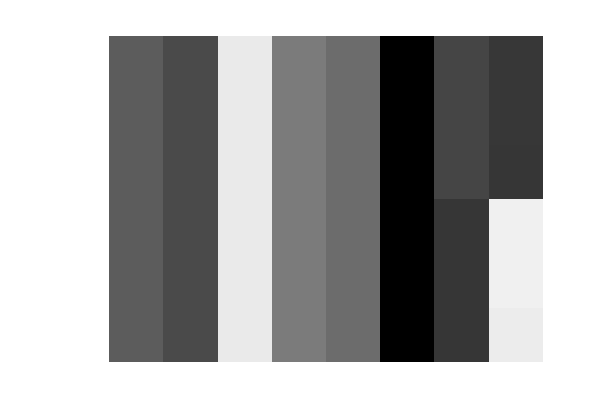

```mathematica
ArrayPlot[Map[IntegerDigits[#,Product[p,{p,{7,11,13,23}}]]&,Take[GoodForTuple[{7,11,13,23}],{130,135}]]]
```

```mathematica
Map[IntegerDigits[#,Product[p,{p,{7,11,13,23}}]]&,Take[GoodForTuple[{7,11,13,23}],{130,135}]]
```

{{13,13538,15073,1776,11029,12276,21240,15469,16655},{13,13538,15073,1776,11029,12276,21240,15469,16656},{13,13538,15073,1776,11029,12276,21240,15469,16775},{13,13538,15073,1776,11029,12276,21241,16769,1225},{13,13538,15073,1776,11029,12276,21241,16769,1226},{13,13538,15073,1776,11029,12276,21241,16769,1564}}

```mathematica
With[
{value= Take[GoodForTuple[{7,11,13,23}],{130,130}][[1]],
tuple={7,11,13,23}
},
With[{
front=Table[
Take[IntegerDigits[value,p],27],{p,{7,11,13,23}}]},
Table[
Sum[front[[i,j]]*tuple[[i]],{i,1,4}],{j,1,27}
]
]
]
```

{183,223,146,339,247,137,105,116,140,46,216,332,94,157,261,158,196,307,114,121,243,250,44,220,339,285,134}

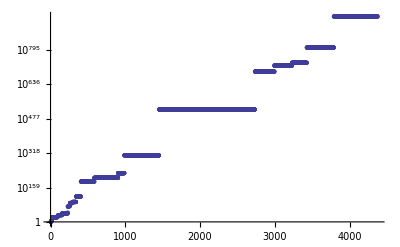

```mathematica
ListLogPlot[GoodForTuple[{3,31,43,173,229}]]
```

```mathematica
FromDigits[Reverse[IntegerDigits[1072636116370398429877656145402334087,7]],7]
```

625175274228757300874855059936848071

```mathematica
IntegerDigits[1072636116370398429877656145402334087,7]
```

{3,3,0,3,2,1,2,1,0,0,3,1,0,2,1,2,0,2,3,0,3,0,1,3,0,2,0,3,2,0,3,3,1,2,3,1,1,3,2,1,0,0,2}

```mathematica
Product[p,{p,{7,11,13,23}}]
```

23023

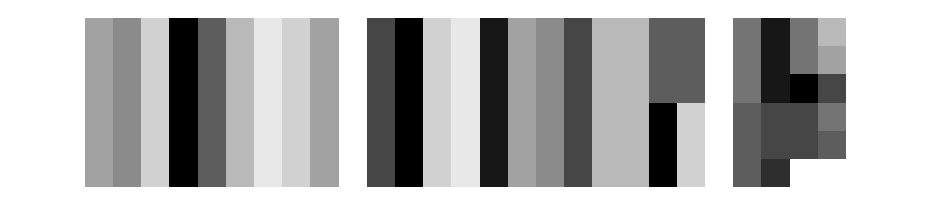

```mathematica
ArrayPlot[Map[IntegerDigits[#,23]&,Take[GoodForTuple[{7,11,13,23}],{130,135}]]]
```

```mathematica
FromDigits[{7,10,13,24,0},67]
```

144125442

```mathematica
Map[IntegerDigits[#,73]&,Take[GoodForTuple[{67,73,83,89}],{6340,6360}]]
```

{{5,5,35,36,13},{5,5,35,36,14},{5,5,35,36,15},{5,5,35,36,16},{5,5,35,36,17},{5,5,35,36,18},{5,5,35,36,19},{5,5,35,36,20},{5,5,35,36,21},{5,5,35,36,22},{5,5,35,36,23},{5,5,35,36,24},{5,5,35,36,25},{5,5,35,36,26},{5,5,35,36,27},{5,5,35,36,28},{5,5,35,36,29},{5,5,35,36,30},{5,5,35,36,31},{5,5,35,36,32},{5,5,35,36,33}}

```mathematica
Map[IntegerDigits[#,83]&,Take[GoodForTuple[{67,73,83,89}],{6340,6360}]]
```

{{3,3,5,8,13},{3,3,5,8,14},{3,3,5,8,15},{3,3,5,8,16},{3,3,5,8,17},{3,3,5,8,18},{3,3,5,8,19},{3,3,5,8,20},{3,3,5,8,21},{3,3,5,8,22},{3,3,5,8,23},{3,3,5,8,24},{3,3,5,8,25},{3,3,5,8,26},{3,3,5,8,27},{3,3,5,8,28},{3,3,5,8,29},{3,3,5,8,30},{3,3,5,8,31},{3,3,5,8,32},{3,3,5,8,33}}

```mathematica
Map[IntegerDigits[#,89]&,Take[GoodForTuple[{67,73,83,89}],{6340,6360}]]
```

{{2,26,39,32,3},{2,26,39,32,4},{2,26,39,32,5},{2,26,39,32,6},{2,26,39,32,7},{2,26,39,32,8},{2,26,39,32,9},{2,26,39,32,10},{2,26,39,32,11},{2,26,39,32,12},{2,26,39,32,13},{2,26,39,32,14},{2,26,39,32,15},{2,26,39,32,16},{2,26,39,32,17},{2,26,39,32,18},{2,26,39,32,19},{2,26,39,32,20},{2,26,39,32,21},{2,26,39,32,22},{2,26,39,32,23}}